## Homework 2 Part 4

### Question 1

The analysis we have assumed that ki=di and nj=2 and a0=0.01 and b0=1 putting theses values into the equation for xs we can define x1s as a function of s

(1+s^2)/(1+s^2/100)

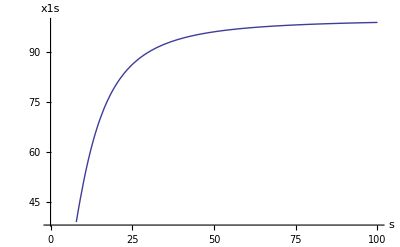

```mathematica
Clear["Global`*"]
F[s_]:=(1+s^2)/(1+s^2/100)
x1s=F[s]
Plot[x1s,{s,0,100},AxesLabel->{"s","x1s"}]
(* We can see that the maximum value of x1s is 100 *)
```

```mathematica
(* Solving for  s for values of x*)
```

```mathematica
NSolve[x1s==50,s]
```

{{s→9.89949},{s→-9.89949}}

```mathematica
NSolve[x1s==5,s]
```

{{s→-2.05196},{s→2.05196}}

```mathematica
NSolve[x1s==95,s]
```

{{s→-43.359},{s→43.359}}

As 100 is the maximum value we should get 5%,50% and 95% activation at 5,50 and 95 respectively as shown above  for positive values of s

### Question 2

Using values of b1=1, a1=100, b2=1 and a2=100, x2s and x3s can be defined as the following functions

```mathematica
F23[x_]:=(1+x^2)/(1+100 x^2)
```

Therefore x2s in terms of s should be the following function;

```mathematica
x2s=FullSimplify[F23[x1s]]
```

(1+((1+s^2)^2)/((1+s^2/100)^2))/(1+(1000000 (1+s^2)^2)/((100+s^2)^2))

And x3s in terms of s should be

```mathematica
x3s=FullSimplify[F23[x2s]]
```

(1+((1+((1+s^2)^2)/((1+s^2/100)^2))^2)/((1+(1000000 (1+s^2)^2)/((100+s^2)^2))^2))/(1+(100 (1+((1+s^2)^2)/((1+s^2/100)^2))^2)/((1+(1000000 (1+s^2)^2)/((100+s^2)^2))^2))

The plot of x2s with respect to s should be as follows:

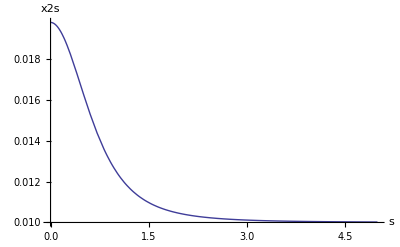

```mathematica
Plot[x2s,{s,0,5},AxesLabel->{"s","x2s"}]
```

Plot of x3s with respect to s

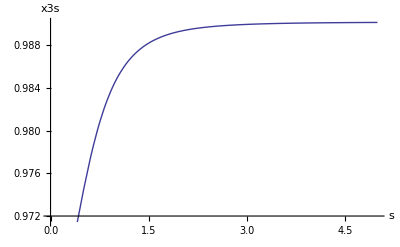

```mathematica
Plot[x3s,{s,0,5},AxesLabel->{"s","x3s"}]
```

Maximum values of x2s and x3s can be evaluated by setting s approaching infinity

```mathematica
maxx2s=Limit[x2s,s-> Infinity]
```

10001/1000001

```mathematica
N[maxx2s]
```

0.010001

Maximum values of x3s can be evaluated in the same way as x2s;

```mathematica
maxx3s=Limit[x3s,s->Infinity]
```

1000102020002/1010004000101

```mathematica
N[maxx3s]
```

0.990196

Basal rate of x2s can be found out by setting s=0, storing value of basal rate in minx2s

```mathematica
minx2s=Limit[x2s,s->0]
N[minx2s]
```

2/101

0.019802

Similarly basal level of x3s can be found out by setting s to 0, and storring the value of basal rate in minx3s

```mathematica
minx3s=Limit[x3s,s->0]
N[minx3s]
```

10205/10601

0.962645

Fold Change with respect to basal level in x2s is

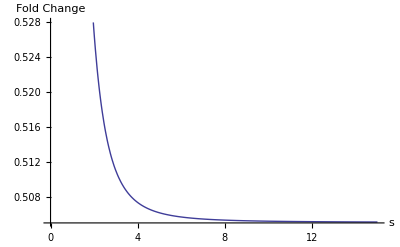

```mathematica
Plot[x2s/minx2s,{s,0,15},AxesLabel-> {"s","Fold Change"}]
```

Fold Change with respect to basal level in x3s is:

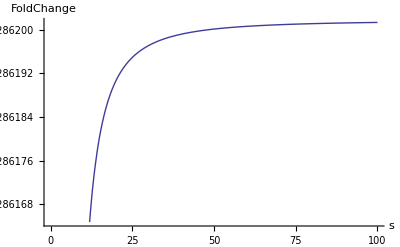

```mathematica
pf31=Plot[x3s/minx3s,{s,0,100}, AxesLabel->{"s","FoldChange"}]
```

To estimate the hill coefficient let us fit the graphs to the following general hill equation:
Y= g0+g1s^n/(g2+s^n)
Here g0 will represent the basal level
and g0+g1 will represent the maximum(or minimum)
Y’= (Y-g0)/g1
g0=basal level
g0+g1= maximum level
therefore
g1=maximum level-basal level
Let Y’=s^n/(g2+s^n)
so 1-Y’=g2/(g2+s^n)
So log(Y'/(1-Y'))=n log s-log g2
and d[log(Y'/(1 - Y'))]/d[log s]= n ; so plotting this result should give us the value of hill coefficient directly.
So all we have to do is find the slope of the plot between log s and log(Y'/(1-Y'))

For x2s the corresponding hill coefficient for activation is:

```mathematica
g0=minx2s;
```

```mathematica
g1=maxx2s-minx2s;
```

```mathematica
y=x2s;
yd=(y-g0)/g1;(*Finding value of Y'*)
```

RowBox[{"LogLinearPlot", "[", RowBox[{StyleBox["f", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["max", "TI"]]}], "}"}]}], "]"}] generates a log-linear plot of StyleBox["f", "TI"] as a function of StyleBox["x", "TI"] from SubscriptBox[StyleBox["x", "TI"], StyleBox["min", "TI"]] to SubscriptBox[StyleBox["x", "TI"], StyleBox["max", "TI"]]. 
RowBox[{"LogLinearPlot", "[", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["f", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["f", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["max", "TI"]]}], "}"}]}], "]"}] generates log-linear plots of several functions SubscriptBox[StyleBox["f", "TI"], StyleBox["i", "TI"]].

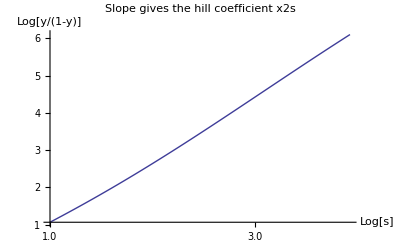

```mathematica
yaxis=Log[yd/(1-yd)];(* Storing the value of log(Y'/(1-Y'))in the variable yaxis*)
yaxisd=D[yaxis,s]/D[Log[s],s];(* d[log(Y'/(1 - Y'))]/d[log s] is stored in this variable *)
?LogLinearPlot
LogLinearPlot[yaxis,{s,1,5},AxesLabel->{"Log[s]","Log[y/(1-y)]"},PlotLabel-> "Slope gives the hill coefficient x2s"]
```

The hill coefficient for x2s when s is near zero:

2.

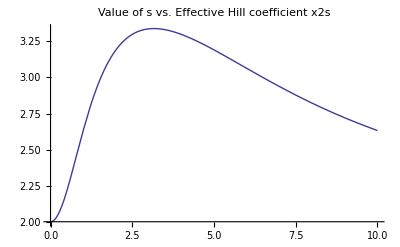

```mathematica
Print["The hill coefficient for x2s when s is near zero:"]
N[Limit[yaxisd,s->0]] (* This will give us the hill coefficient at the time of activation when the value of s is very close to zero *)
Plot[yaxisd,{s,0,10},PlotLabel-> "Value of s vs. Effective Hill coefficient x2s"](* Plotting estimated hill coefficient for *)
```

For x3s the corresponding hill coefficient for activation is:

```mathematica
g03=minx3s;
```

```mathematica
g13=maxx3s-minx3s;
```

```mathematica
y3=x3s;
yd3=(y3-g03)/g13;(*Finding value of Y'*)
```

RowBox[{"LogLinearPlot", "[", RowBox[{StyleBox["f", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["max", "TI"]]}], "}"}]}], "]"}] generates a log-linear plot of StyleBox["f", "TI"] as a function of StyleBox["x", "TI"] from SubscriptBox[StyleBox["x", "TI"], StyleBox["min", "TI"]] to SubscriptBox[StyleBox["x", "TI"], StyleBox["max", "TI"]]. 
RowBox[{"LogLinearPlot", "[", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["f", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["f", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["max", "TI"]]}], "}"}]}], "]"}] generates log-linear plots of several functions SubscriptBox[StyleBox["f", "TI"], StyleBox["i", "TI"]].

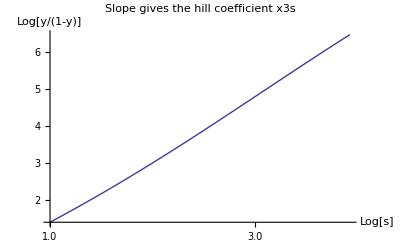

```mathematica
yaxis3=Log[yd3/(1-yd3)];(* Storing the value of log(Y'/(1-Y'))in the variable yaxis*)
yaxisd3=D[yaxis3,s]/D[Log[s],s];(* d[log(Y'/(1 - Y'))]/d[log s] is stored in this variable *)
?LogLinearPlot
LogLinearPlot[yaxis3,{s,1,5},AxesLabel->{"Log[s]","Log[y/(1-y)]"},PlotLabel->"Slope gives the hill coefficient x3s"]
```

The hill coefficient for x3s when s is near zero:

2.

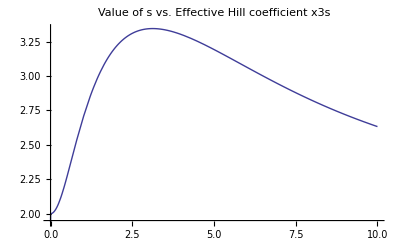

```mathematica
Print["The hill coefficient for x3s when s is near zero:"]
N[Limit[yaxisd3,s->0]] (* This will give us the hill coefficient at the time of activation when the value of s is very close to zero *)
Plot[yaxisd3,{s,0,10},PlotLabel-> "Value of s vs. Effective Hill coefficient x3s"](* Plotting estimated hill coefficient for *)
```

### Question 3

Defining additional function to find value of x2s according to b1=0.01 and a1=1

```mathematica
F21[x_]:=(1+x^2/100)/(1+x^2)
```

Implementing these new values lead to the following new results:
We see an increase in Fold change for x3s and increased hill coefficient for intermediate values of s  as shown below:

Therefore x2s in terms of s should be the following function;

```mathematica
x2s=FullSimplify[F21[x1s]]
```

(10100+400 s^2+101 s^4)/(20000+20200 s^2+10001 s^4)

And x3s in terms of s should be

```mathematica
x3s=FullSimplify[F23[x2s]]
```

(1+((10100+400 s^2+101 s^4)^2)/((20000+20200 s^2+10001 s^4)^2))/(1+(100 (10100+400 s^2+101 s^4)^2)/((20000+20200 s^2+10001 s^4)^2))

The plot of x2s with respect to s should be as follows:

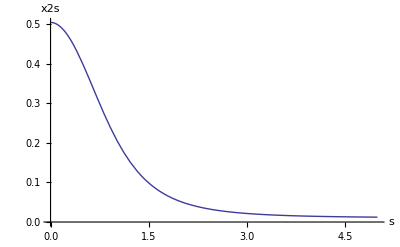

```mathematica
Plot[x2s,{s,0,5},AxesLabel->{"s","x2s"}]
```

Plot of x3s with respect to s

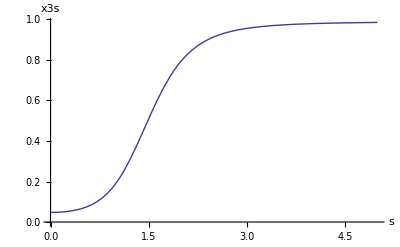

```mathematica
Plot[x3s,{s,0,5},AxesLabel->{"s","x3s"}]
```

Maximum values of x2s and x3s can be evaluated by setting s approaching infinity

```mathematica
maxx2s=Limit[x2s,s-> Infinity]
```

101/10001

```mathematica
N[maxx2s]
```

0.010099

Maximum values of x3s can be evaluated in the same way as x2s;

```mathematica
maxx3s=Limit[x3s,s->Infinity]
```

100030202/101040101

```mathematica
N[maxx3s]
```

0.990005

Basal rate of x2s can be found out by setting s=0, storing value of basal rate in minx2s

```mathematica
minx2s=Limit[x2s,s->0]
N[minx2s]
```

101/200

0.505

Similarly basal level of x3s can be found out by setting s to 0, and storring the value of basal rate in minx3s

```mathematica
minx3s=Limit[x3s,s->0]
N[minx3s]
```

50201/1060100

0.047355

Fold Change with respect to basal level in x2s is

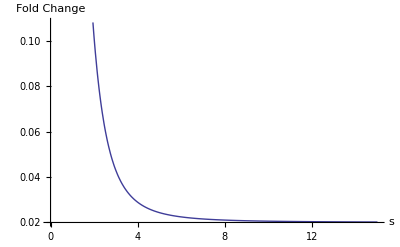

```mathematica
Plot[x2s/minx2s,{s,0,15},AxesLabel-> {"s","Fold Change"}]
```

We see the fold change for x2s is even lower than in the previous case.

Fold Change with respect to basal level in x3s is:

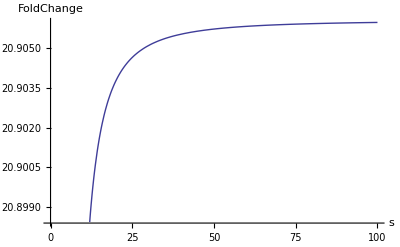

```mathematica
pf32=Plot[x3s/minx3s,{s,0,100}, AxesLabel->{"s","FoldChange"}]
```

We see here that the fold change is almost twenty times the fold change seen for the previous parameter values.

To estimate the hill coefficient let us fit the graphs to the following general hill equation:
Y= g0+g1s^n/(g2+s^n)
Here g0 will represent the basal level
and g0+g1 will represent the maximum(or minimum)
Y’= (Y-g0)/g1
g0=basal level
g0+g1= maximum level
therefore
g1=maximum level-basal level
Let Y’=s^n/(g2+s^n)
so 1-Y’=g2/(g2+s^n)
So log(Y'/(1-Y'))=n log s-log g2
and d[log(Y'/(1 - Y'))]/d[log s]= n ; so plotting this result should give us the value of hill coefficient directly.
So all we have to do is find the slope of the plot between log s and log(Y'/(1-Y'))

For x2s the corresponding hill coefficient for activation is:

```mathematica
g0=minx2s;
```

```mathematica
g1=maxx2s-minx2s;
```

```mathematica
y=x2s;
yd=(y-g0)/g1;(*Finding value of Y'*)
```

RowBox[{"LogLinearPlot", "[", RowBox[{StyleBox["f", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["max", "TI"]]}], "}"}]}], "]"}] generates a log-linear plot of StyleBox["f", "TI"] as a function of StyleBox["x", "TI"] from SubscriptBox[StyleBox["x", "TI"], StyleBox["min", "TI"]] to SubscriptBox[StyleBox["x", "TI"], StyleBox["max", "TI"]]. 
RowBox[{"LogLinearPlot", "[", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["f", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["f", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["max", "TI"]]}], "}"}]}], "]"}] generates log-linear plots of several functions SubscriptBox[StyleBox["f", "TI"], StyleBox["i", "TI"]].

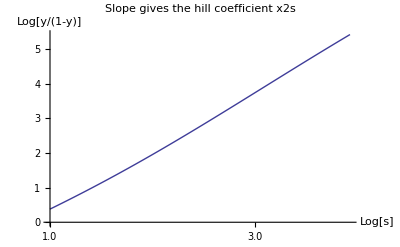

```mathematica
yaxis=Log[yd/(1-yd)];(* Storing the value of log(Y'/(1-Y'))in the variable yaxis*)
yaxisd=D[yaxis,s]/D[Log[s],s];(* d[log(Y'/(1 - Y'))]/d[log s] is stored in this variable *)
?LogLinearPlot
LogLinearPlot[yaxis,{s,1,5},AxesLabel->{"Log[s]","Log[y/(1-y)]"},PlotLabel-> "Slope gives the hill coefficient x2s"]
```

The hill coefficient for x2s when s is near zero:

2.

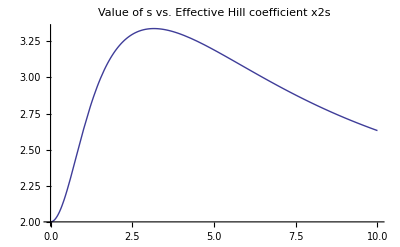

```mathematica
Print["The hill coefficient for x2s when s is near zero:"]
N[Limit[yaxisd,s->0]] (* This will give us the hill coefficient at the time of activation when the value of s is very close to zero *)
Plot[yaxisd,{s,0,10},PlotLabel-> "Value of s vs. Effective Hill coefficient x2s"](* Plotting estimated hill coefficient for *)
```

For x3s the corresponding hill coefficient for activation is:

```mathematica
g03=minx3s;
```

```mathematica
g13=maxx3s-minx3s;
```

```mathematica
y3=x3s;
yd3=(y3-g03)/g13;(*Finding value of Y'*)
```

RowBox[{"LogLinearPlot", "[", RowBox[{StyleBox["f", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["max", "TI"]]}], "}"}]}], "]"}] generates a log-linear plot of StyleBox["f", "TI"] as a function of StyleBox["x", "TI"] from SubscriptBox[StyleBox["x", "TI"], StyleBox["min", "TI"]] to SubscriptBox[StyleBox["x", "TI"], StyleBox["max", "TI"]]. 
RowBox[{"LogLinearPlot", "[", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["f", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["f", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["max", "TI"]]}], "}"}]}], "]"}] generates log-linear plots of several functions SubscriptBox[StyleBox["f", "TI"], StyleBox["i", "TI"]].

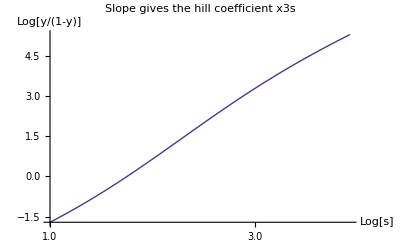

```mathematica
yaxis3=Log[yd3/(1-yd3)];(* Storing the value of log(Y'/(1-Y'))in the variable yaxis*)
yaxisd3=D[yaxis3,s]/D[Log[s],s];(* d[log(Y'/(1 - Y'))]/d[log s] is stored in this variable *)
?LogLinearPlot
LogLinearPlot[yaxis3,{s,1,5},AxesLabel->{"Log[s]","Log[y/(1-y)]"},PlotLabel->"Slope gives the hill coefficient x3s",PlotRange->Full]
```

The hill coefficient for x3s when s is near zero:

2.

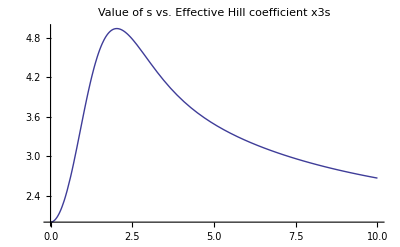

```mathematica
Print["The hill coefficient for x3s when s is near zero:"]
N[Limit[yaxisd3,s->0]] (* This will give us the hill coefficient at the time of activation when the value of s is very close to zero *)
Plot[yaxisd3,{s,0,10},PlotRange->Full,PlotLabel-> "Value of s vs. Effective Hill coefficient x3s"](* Plotting estimated hill coefficient for *)
```

### Question 4 & 5 (Implementation of an App)

To see what would be the minimum and maximum values of the hill coefficient we can define the following new functions with the value of a1,b1,a2,b2 undefined and see what happens to the overall graph for hill coefficient

```mathematica
Manipulate[Module[{},
Fa[s_]:=(1+s^2)/(1+s^2/100);
x1s=Fa[s];
F21a[x_]:=(1+b1*x^2 )/(1+a1*x^2);
F23a[x_]:= (1+b2*x^2 )/(1+a2*x^2);
x2s=FullSimplify[F21a[x1s]];
x3s=FullSimplify[F23a[x2s]];
minx3s=Limit[x3s,s->0];
maxx3s=Limit[x3s,s->Infinity];
g03=minx3s;
g13=maxx3s-minx3s;
y3=x3s;
yd3=(y3-g03)/g13;(*Finding value of Y'*)
yaxis3=Log[yd3/(1-yd3)];(* Storing the value of log(Y'/(1-Y'))in the variable yaxis*)
yaxisd3=D[yaxis3,s]/D[Log[s],s];(* d[log(Y'/(1 - Y'))]/d[log s] is stored in this variable *)

LogLinearPlot[yaxis3,{s,1,5},AxesLabel->{"Log[s]","Log[y/(1-y)]"},PlotLabel->"Slope gives the hill coefficient",ImageSize->300]

Plot[yaxisd3,{s,0,10},PlotRange->Full,PlotLabel-> "Value of s vs. Effective Hill coefficient x3s",AxesLabel->{"s","n Hill coefficient"},ImageSize->300]

Plot[x3s/minx3s,{s,0,10},PlotLabel->"Fold Change for x3s",AxesLabel->{"s","Fold Change"},ImageSize-> 300]

],{a1,1,100,1,Appearance->"Open"},{a2,1,1000,10,Appearance->"Open"},{b1,0.00001,1,0.0001,Appearance->"Open"},{b2,0.00001,1,0.0001,Appearance->"Open"},FrameLabel->"An App to see the Value of Hill coefficient when values of a1,a2,b2,b2 are changed",
AppearanceElements-> All]
```

From the above Application the user can make the following conclusions:

1. Increasing the value of a1 decreases the fold change and does not have a significant effect on the Hill Coefficient Plot
2. Increasing the value of a2 increases the fold change appreciably and does not have a significant effect on the Hill Coefficient Plot 
3. Increasing the value of b1 decreases both the Hill Coefficient plot and the Fold change 
4. Increasing b2 does not have a significant effect on the Hill Coefficient plot and decreases the fold change.
5. The maximum hill coefficient is obtained for values of b2 much smaller that a1 and a2 and the minimum when the value of b2 approaches that of a1 and a2.